{2011,11,15,10,24,22.0976562}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`12 recursive bisections in TraditionalForm`t near TraditionalForm`{t} = TraditionalForm`{74.023}. NIntegrate obtained TraditionalForm`-0.00180669 and TraditionalForm`2.8803554063824867`*^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`12 recursive bisections in TraditionalForm`t near TraditionalForm`{t} = TraditionalForm`{74.023}. NIntegrate obtained TraditionalForm`-0.00196087 and TraditionalForm`4.39362473949269`*^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`12 recursive bisections in TraditionalForm`t near TraditionalForm`{t} = TraditionalForm`{5.74057}. NIntegrate obtained TraditionalForm`-0.000621882 and TraditionalForm`1.610636706074921`*^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

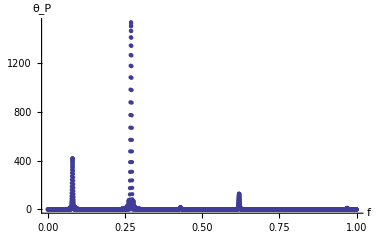

{2011,11,15,11,44,36.2841796}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`12 recursive bisections in TraditionalForm`t near TraditionalForm`{t} = TraditionalForm`{74.023}. NIntegrate obtained TraditionalForm`0.0010668832693203458` and TraditionalForm`1.4372697089787046`*^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`12 recursive bisections in TraditionalForm`t near TraditionalForm`{t} = TraditionalForm`{74.023}. NIntegrate obtained TraditionalForm`0.00013586669091786296` and TraditionalForm`3.110156929860199`*^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`12 recursive bisections in TraditionalForm`t near TraditionalForm`{t} = TraditionalForm`{74.023}. NIntegrate obtained TraditionalForm`0.0006690791809814411` and TraditionalForm`2.8085706444844574`*^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

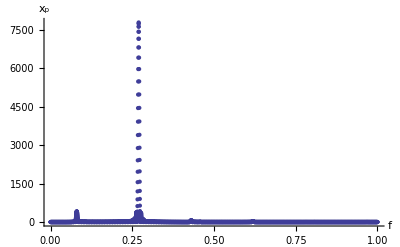

{2011,11,15,12,18,25.9951171}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`12 recursive bisections in TraditionalForm`t near TraditionalForm`{t} = TraditionalForm`{74.023}. NIntegrate obtained TraditionalForm`-0.0141366 and TraditionalForm`2.6491821109768332`*^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`12 recursive bisections in TraditionalForm`t near TraditionalForm`{t} = TraditionalForm`{74.023}. NIntegrate obtained TraditionalForm`0.022019475091491214` and TraditionalForm`2.3784530865601034`*^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`12 recursive bisections in TraditionalForm`t near TraditionalForm`{t} = TraditionalForm`{74.023}. NIntegrate obtained TraditionalForm`0.00021087720156617862` and TraditionalForm`2.1644170072844476`*^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

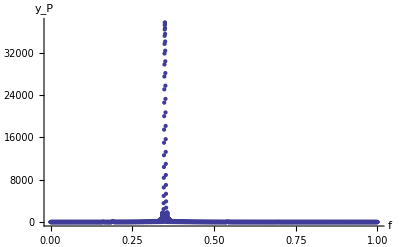

{2011,11,15,12,51,22.2861328}

```mathematica
Date[]
g=9.8;k=0.1;m=0.02;L0=1;tm=200;
xinitial={0,1.3};yinitial={-L0,0};
equs={m x''[t]==-k x[t] (1-L0/(√(x[t]^2+y[t]^2))),
m y''[t]==k y[t] (-1+L0/(√(x[t]^2+y[t]^2)))-m g,
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],
y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equs,{x,y},{t,0,tm},MaxSteps->∞];
{x,y}={x,y}/.s[[1]];
θ[t_]:=Arg[-y[t]+x[t]*ⅈ];const=2.0π;
(*--------------------------------------------*)
fs=ps={};
Do[
real=NIntegrate[θ[t]*Cos[const f t],
{t,0,tm},MaxRecursion->12];
imaginary=NIntegrate[θ[t]*Sin[const f t],
{t,0,tm},MaxRecursion->12];
AppendTo[fs,{f,real-imaginary ⅈ}];
AppendTo[ps,{f,real^2+imaginary^2}],
{f,0,1,0.0002}]
ListPlot[ps,PlotRange->All,AxesLabel->{"f","θ_P"}]
Export["e:/data/thetafs.dat",fs];
Export["e:/data/thetaps.dat",ps];
Date[]
(*--------------------------------------------*)
fs=ps={};
Do[
real=NIntegrate[x[t]*Cos[const f t],
{t,0,tm},MaxRecursion->12];
imaginary=NIntegrate[x[t]*Sin[const f t],
{t,0,tm},MaxRecursion->12];
AppendTo[fs,{f,real-imaginary ⅈ}];
AppendTo[ps,{f,real^2+imaginary^2}],
{f,0,1,0.0002}]
ListPlot[ps,PlotRange->All,AxesLabel->{"f","x_p"}]
Export["e:/data/xfs.dat",fs];
Export["e:/data/xps.dat",ps];
Date[]
(*--------------------------------------------*)
fs=ps={};
sample=2000;(*points of sampling*)
average=NSum[y[t],{t,0,tm,tm/sample}]/(sample+1);
Do[
real=NIntegrate[(y[t]-average)*Cos[const f t],
{t,0,tm},MaxRecursion->12];
imaginary=NIntegrate[(y[t]-average)*Sin[const f t],
{t,0,tm},MaxRecursion->12];
AppendTo[fs,{f,real-imaginary ⅈ}];
AppendTo[ps,{f,real^2+imaginary^2}],
{f,0,1,0.0002}]
ListPlot[ps,PlotRange->All,AxesLabel->{"f","y_P"}]
Export["e:/data/yfs.dat",fs];
Export["e:/data/yps.dat",ps];
Date[]
Clear[x,y,θ]
```